```mathematica
FourStepCircleStatesToPositionProbability[State0_]:=
Module[{State=State0},
ProbabilityAll = Simplify[Conjugate[State]*State];
ProbabilaityMixed = Transpose[{{
ProbabilityAll[[1,1]] + ProbabilityAll[[2,1]] + ProbabilityAll[[3,1]],
ProbabilityAll[[4,1]] + ProbabilityAll[[5,1]] + ProbabilityAll[[6,1]],
ProbabilityAll[[7,1]] + ProbabilityAll[[8,1]] + ProbabilityAll[[9,1]],
ProbabilityAll[[10,1]] + ProbabilityAll[[11,1]] + ProbabilityAll[[12,1]]
}}];
For[k=1,k≤(Dimensions[ProbabilityAll]⟦1⟧)/BitOrder,k++,∑_(j=(BitOrder (k-1))+1)^(BitOrder k) ProbabilityAll⟦j,1⟧
];
Return[ProbabilaityMixed];
]
```

```mathematica
LazyQuantumRandomWalkHistory[State0_,Steps0_,Type0_,History0_,ReturnType0_]:=
Module[{
State=State0,(* 12x1 matrix with input state *)
Steps=Steps0, (* Number of itterations to perform *)
Type=Type0,(* 0:Standard, 1:Odd's, 2:Even's, 3:Average's *)
HistoryArray=History0,(* 0:Final State, 1:History *)
ReturnType=ReturnType0 (* 0:States, 1:Position Probabilities *)
},
History={};
BitOrder=3;
σ=ⅇ^((π 2 ⅈ)/BitOrder);
({{a, b, c}, {d, e, f}, {g, h, i}})=H=({{1, 1, 1}, {1, σ^(BitOrder-1), σ}, {1, σ, σ^(BitOrder-1)}})/(√BitOrder);
M=Transpose[({{a, 0, 0, 0, b, 0, 0, 0, 0, 0, 0, c}, {d, 0, 0, 0, e, 0, 0, 0, 0, 0, 0, f}, {g, 0, 0, 0, h, 0, 0, 0, 0, 0, 0, i}, {0, 0, c, a, 0, 0, 0, b, 0, 0, 0, 0}, {0, 0, f, d, 0, 0, 0, e, 0, 0, 0, 0}, {0, 0, i, g, 0, 0, 0, h, 0, 0, 0, 0}, {0, 0, 0, 0, 0, c, a, 0, 0, 0, b, 0}, {0, 0, 0, 0, 0, f, d, 0, 0, 0, e, 0}, {0, 0, 0, 0, 0, i, g, 0, 0, 0, h, 0}, {0, b, 0, 0, 0, 0, 0, 0, c, a, 0, 0}, {0, e, 0, 0, 0, 0, 0, 0, f, d, 0, 0}, {0, h, 0, 0, 0, 0, 0, 0, i, g, 0, 0}})];
AppendTo[History,State];
For[j=0,j<Steps,j++,
State=Simplify[M.State];
If[HistoryArray==1||Type==3,AppendTo[History,State]]
];
If[HistoryArray==1,
If[ReturnType==0,
Return[History],
Return[
Map[FourStepCircleStatesToPositionProbability,
History]]],
If[ReturnType==0,
Return[State],
Return[
FourStepCircleStatesToPositionProbability[State]]];
]]
```

```mathematica
LQRWHistorgramPositionProbabilities[State0_,Steps0_]:=
Module[{State=State0,Steps=Steps0},
Return[
Map[Flatten,
Map[FourStepCircleStatesToPositionProbability,
LazyQuantumRandomWalkHistory[State,Steps,0,1,0]]]]]
```

```mathematica
CumulativeMean[List0_]:=
Module[{List=List0},
Return[
(Accumulate[#]/Range[Length[#]])
&/@List]]
```

```mathematica
y=.;x=.;
y=Sqrt[(1-x^2)/2];
```

```mathematica
Results=Transpose[Table[
Map[Last,
CumulativeMean[Transpose[
LQRWHistorgramPositionProbabilities[
SparseArray[
{{12,1}->0,
{1,1}->x,
{2,1}->Sqrt[(1-x^2)/2],
{3,1}->Sqrt[(1-x^2)/2]}
],
100]]]],
{x,0.5,1,.005}]];
```

{{0.303126+0. ⅈ,0.303317+0. ⅈ,0.303508+0. ⅈ,0.303698+0. ⅈ,0.303888+0. ⅈ,0.304077+0. ⅈ,0.304266+0. ⅈ,0.304454+0. ⅈ,0.304642+0. ⅈ,0.304829+0. ⅈ,0.305016+0. ⅈ,0.305202+0. ⅈ,0.305387+0. ⅈ,0.305571+0. ⅈ,0.305755+0. ⅈ,0.305938+0. ⅈ,0.30612+0. ⅈ,0.306301+0. ⅈ,0.306482+0. ⅈ,0.306661+0. ⅈ,0.30684+0. ⅈ,0.307017+0. ⅈ,0.307194+0. ⅈ,0.307369+0. ⅈ,0.307544+0. ⅈ,0.307717+0. ⅈ,0.30789+0. ⅈ,0.308061+0. ⅈ,0.30823+0. ⅈ,0.308399+0. ⅈ,0.308566+0. ⅈ,0.308732+0. ⅈ,0.308897+0. ⅈ,0.30906+0. ⅈ,0.309221+0. ⅈ,0.309381+0. ⅈ,0.30954+0. ⅈ,0.309696+0. ⅈ,0.309851+0. ⅈ,0.310005+0. ⅈ,0.310156+0. ⅈ,0.310306+0. ⅈ,0.310453+0. ⅈ,0.310599+0. ⅈ,0.310743+0. ⅈ,0.310884+0. ⅈ,0.311023+0. ⅈ,0.31116+0. ⅈ,0.311295+0. ⅈ,0.311427+0. ⅈ,0.311557+0. ⅈ,0.311684+0. ⅈ,0.311808+0. ⅈ,0.311929+0. ⅈ,0.312048+0. ⅈ,0.312164+0. ⅈ,0.312276+0. ⅈ,0.312385+0. ⅈ,0.312491+0. ⅈ,0.312594+0. ⅈ,0.312693+0. ⅈ,0.312788+0. ⅈ,0.312879+0. ⅈ,0.312966+0. ⅈ,0.313049+0. ⅈ,0.313127+0. ⅈ,0.313201+0. ⅈ,0.31327+0. ⅈ,0.313335+0. ⅈ,0.313393+0. ⅈ,0.313447+0. ⅈ,0.313494+0. ⅈ,0.313536+0. ⅈ,0.313571+0. ⅈ,0.3136+0. ⅈ,0.313621+0. ⅈ,0.313635+0. ⅈ,0.313641+0. ⅈ,0.313639+0. ⅈ,0.313627+0. ⅈ,0.313606+0. ⅈ,0.313575+0. ⅈ,0.313533+0. ⅈ,0.313479+0. ⅈ,0.313412+0. ⅈ,0.313331+0. ⅈ,0.313235+0. ⅈ,0.313121+0. ⅈ,0.31299+0. ⅈ,0.312837+0. ⅈ,0.31266+0. ⅈ,0.312457+0. ⅈ,0.312221+0. ⅈ,0.311949+0. ⅈ,0.311632+0. ⅈ,0.311258+0. ⅈ,0.310812+0. ⅈ,0.310263+0. ⅈ,0.309557+0. ⅈ,0.308552+0. ⅈ,0.305769+0. ⅈ},{0.196985+0. ⅈ,0.196792+0. ⅈ,0.196599+0. ⅈ,0.196406+0. ⅈ,0.196215+0. ⅈ,0.196023+0. ⅈ,0.195832+0. ⅈ,0.195642+0. ⅈ,0.195452+0. ⅈ,0.195263+0. ⅈ,0.195074+0. ⅈ,0.194886+0. ⅈ,0.194699+0. ⅈ,0.194513+0. ⅈ,0.194327+0. ⅈ,0.194142+0. ⅈ,0.193957+0. ⅈ,0.193774+0. ⅈ,0.193591+0. ⅈ,0.19341+0. ⅈ,0.193229+0. ⅈ,0.193049+0. ⅈ,0.19287+0. ⅈ,0.192692+0. ⅈ,0.192515+0. ⅈ,0.19234+0. ⅈ,0.192165+0. ⅈ,0.191992+0. ⅈ,0.191819+0. ⅈ,0.191648+0. ⅈ,0.191479+0. ⅈ,0.191311+0. ⅈ,0.191144+0. ⅈ,0.190978+0. ⅈ,0.190814+0. ⅈ,0.190652+0. ⅈ,0.190491+0. ⅈ,0.190332+0. ⅈ,0.190174+0. ⅈ,0.190018+0. ⅈ,0.189864+0. ⅈ,0.189712+0. ⅈ,0.189562+0. ⅈ,0.189414+0. ⅈ,0.189268+0. ⅈ,0.189124+0. ⅈ,0.188982+0. ⅈ,0.188842+0. ⅈ,0.188705+0. ⅈ,0.18857+0. ⅈ,0.188438+0. ⅈ,0.188308+0. ⅈ,0.188182+0. ⅈ,0.188057+0. ⅈ,0.187936+0. ⅈ,0.187818+0. ⅈ,0.187703+0. ⅈ,0.187591+0. ⅈ,0.187482+0. ⅈ,0.187377+0. ⅈ,0.187275+0. ⅈ,0.187177+0. ⅈ,0.187083+0. ⅈ,0.186994+0. ⅈ,0.186908+0. ⅈ,0.186827+0. ⅈ,0.18675+0. ⅈ,0.186678+0. ⅈ,0.186611+0. ⅈ,0.186549+0. ⅈ,0.186493+0. ⅈ,0.186443+0. ⅈ,0.186398+0. ⅈ,0.18636+0. ⅈ,0.186329+0. ⅈ,0.186305+0. ⅈ,0.186288+0. ⅈ,0.186279+0. ⅈ,0.186279+0. ⅈ,0.186287+0. ⅈ,0.186306+0. ⅈ,0.186334+0. ⅈ,0.186373+0. ⅈ,0.186425+0. ⅈ,0.186489+0. ⅈ,0.186567+0. ⅈ,0.18666+0. ⅈ,0.186771+0. ⅈ,0.1869+0. ⅈ,0.18705+0. ⅈ,0.187224+0. ⅈ,0.187425+0. ⅈ,0.187657+0. ⅈ,0.187927+0. ⅈ,0.188242+0. ⅈ,0.188613+0. ⅈ,0.189058+0. ⅈ,0.189604+0. ⅈ,0.190309+0. ⅈ,0.191312+0. ⅈ,0.194098+0. ⅈ},{0.302905+0. ⅈ,0.3031+0. ⅈ,0.303295+0. ⅈ,0.303489+0. ⅈ,0.303683+0. ⅈ,0.303876+0. ⅈ,0.304069+0. ⅈ,0.304262+0. ⅈ,0.304453+0. ⅈ,0.304645+0. ⅈ,0.304835+0. ⅈ,0.305025+0. ⅈ,0.305215+0. ⅈ,0.305404+0. ⅈ,0.305592+0. ⅈ,0.305779+0. ⅈ,0.305965+0. ⅈ,0.306151+0. ⅈ,0.306336+0. ⅈ,0.30652+0. ⅈ,0.306703+0. ⅈ,0.306885+0. ⅈ,0.307066+0. ⅈ,0.307246+0. ⅈ,0.307425+0. ⅈ,0.307604+0. ⅈ,0.30778+0. ⅈ,0.307956+0. ⅈ,0.308131+0. ⅈ,0.308304+0. ⅈ,0.308476+0. ⅈ,0.308647+0. ⅈ,0.308816+0. ⅈ,0.308984+0. ⅈ,0.30915+0. ⅈ,0.309315+0. ⅈ,0.309479+0. ⅈ,0.30964+0. ⅈ,0.3098+0. ⅈ,0.309959+0. ⅈ,0.310115+0. ⅈ,0.31027+0. ⅈ,0.310422+0. ⅈ,0.310573+0. ⅈ,0.310722+0. ⅈ,0.310869+0. ⅈ,0.311013+0. ⅈ,0.311155+0. ⅈ,0.311295+0. ⅈ,0.311432+0. ⅈ,0.311567+0. ⅈ,0.311699+0. ⅈ,0.311829+0. ⅈ,0.311956+0. ⅈ,0.31208+0. ⅈ,0.312201+0. ⅈ,0.312319+0. ⅈ,0.312433+0. ⅈ,0.312545+0. ⅈ,0.312653+0. ⅈ,0.312757+0. ⅈ,0.312858+0. ⅈ,0.312954+0. ⅈ,0.313047+0. ⅈ,0.313135+0. ⅈ,0.313219+0. ⅈ,0.313299+0. ⅈ,0.313374+0. ⅈ,0.313443+0. ⅈ,0.313508+0. ⅈ,0.313567+0. ⅈ,0.31362+0. ⅈ,0.313667+0. ⅈ,0.313708+0. ⅈ,0.313742+0. ⅈ,0.313769+0. ⅈ,0.313789+0. ⅈ,0.3138+0. ⅈ,0.313804+0. ⅈ,0.313798+0. ⅈ,0.313783+0. ⅈ,0.313757+0. ⅈ,0.31372+0. ⅈ,0.313672+0. ⅈ,0.313611+0. ⅈ,0.313535+0. ⅈ,0.313444+0. ⅈ,0.313337+0. ⅈ,0.31321+0. ⅈ,0.313063+0. ⅈ,0.312892+0. ⅈ,0.312693+0. ⅈ,0.312464+0. ⅈ,0.312196+0. ⅈ,0.311884+0. ⅈ,0.311515+0. ⅈ,0.311073+0. ⅈ,0.310528+0. ⅈ,0.309826+0. ⅈ,0.308823+0. ⅈ,0.306036+0. ⅈ},{0.196985+0. ⅈ,0.196792+0. ⅈ,0.196599+0. ⅈ,0.196406+0. ⅈ,0.196215+0. ⅈ,0.196023+0. ⅈ,0.195832+0. ⅈ,0.195642+0. ⅈ,0.195452+0. ⅈ,0.195263+0. ⅈ,0.195074+0. ⅈ,0.194886+0. ⅈ,0.194699+0. ⅈ,0.194513+0. ⅈ,0.194327+0. ⅈ,0.194142+0. ⅈ,0.193957+0. ⅈ,0.193774+0. ⅈ,0.193591+0. ⅈ,0.19341+0. ⅈ,0.193229+0. ⅈ,0.193049+0. ⅈ,0.19287+0. ⅈ,0.192692+0. ⅈ,0.192515+0. ⅈ,0.19234+0. ⅈ,0.192165+0. ⅈ,0.191992+0. ⅈ,0.191819+0. ⅈ,0.191648+0. ⅈ,0.191479+0. ⅈ,0.191311+0. ⅈ,0.191144+0. ⅈ,0.190978+0. ⅈ,0.190814+0. ⅈ,0.190652+0. ⅈ,0.190491+0. ⅈ,0.190332+0. ⅈ,0.190174+0. ⅈ,0.190018+0. ⅈ,0.189864+0. ⅈ,0.189712+0. ⅈ,0.189562+0. ⅈ,0.189414+0. ⅈ,0.189268+0. ⅈ,0.189124+0. ⅈ,0.188982+0. ⅈ,0.188842+0. ⅈ,0.188705+0. ⅈ,0.18857+0. ⅈ,0.188438+0. ⅈ,0.188308+0. ⅈ,0.188182+0. ⅈ,0.188057+0. ⅈ,0.187936+0. ⅈ,0.187818+0. ⅈ,0.187703+0. ⅈ,0.187591+0. ⅈ,0.187482+0. ⅈ,0.187377+0. ⅈ,0.187275+0. ⅈ,0.187177+0. ⅈ,0.187083+0. ⅈ,0.186994+0. ⅈ,0.186908+0. ⅈ,0.186827+0. ⅈ,0.18675+0. ⅈ,0.186678+0. ⅈ,0.186611+0. ⅈ,0.186549+0. ⅈ,0.186493+0. ⅈ,0.186443+0. ⅈ,0.186398+0. ⅈ,0.18636+0. ⅈ,0.186329+0. ⅈ,0.186305+0. ⅈ,0.186288+0. ⅈ,0.186279+0. ⅈ,0.186279+0. ⅈ,0.186287+0. ⅈ,0.186306+0. ⅈ,0.186334+0. ⅈ,0.186373+0. ⅈ,0.186425+0. ⅈ,0.186489+0. ⅈ,0.186567+0. ⅈ,0.18666+0. ⅈ,0.186771+0. ⅈ,0.1869+0. ⅈ,0.18705+0. ⅈ,0.187224+0. ⅈ,0.187425+0. ⅈ,0.187657+0. ⅈ,0.187927+0. ⅈ,0.188242+0. ⅈ,0.188613+0. ⅈ,0.189058+0. ⅈ,0.189604+0. ⅈ,0.190309+0. ⅈ,0.191312+0. ⅈ,0.194098+0. ⅈ}}

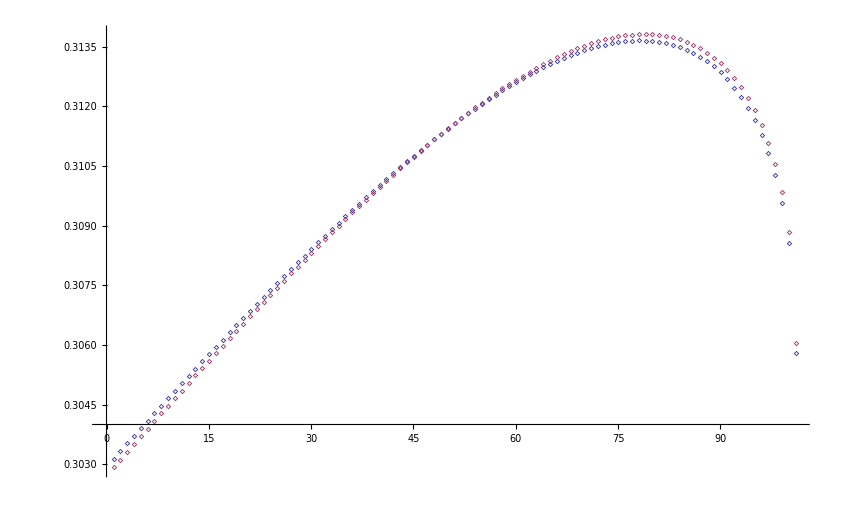

```mathematica
ListPlot[Results[[{1,3}]],
PlotMarkers->{"⋄","⋄","⋄","⋄"}]
```

```mathematica
Max[Re[Results]]
```

0.313804

```mathematica
ThreeKUpperHalf=Re[{{0.3031258414270467+0. ⅈ,0.3033170498393522+0. ⅈ,0.30350783174550455+0. ⅈ,0.30369816337724687+0. ⅈ,0.3038880205531466+0. ⅈ,0.3040773786642674+0. ⅈ,0.3042662126592126+0. ⅈ,0.30445449702847466+0. ⅈ,0.3046422057880916+0. ⅈ,0.30482931246255296+0. ⅈ,0.3050157900668957+0. ⅈ,0.3052016110879554+0. ⅈ,0.30538674746474037+0. ⅈ,0.3055711705678391+0. ⅈ,0.30575485117781737+0. ⅈ,0.3059377594625678+0. ⅈ,0.3061198649534886+0. ⅈ,0.30630113652048535+0. ⅈ,0.30648154234565056+0. ⅈ,0.3066610498956047+0. ⅈ,0.3068396258923415+0. ⅈ,0.30701723628253275+0. ⅈ,0.307193846205164+0. ⅈ,0.30736941995736716+0. ⅈ,0.3075439209583794+0. ⅈ,0.3077173117114349+0. ⅈ,0.3078895537634765+0. ⅈ,0.3080606076625289+0. ⅈ,0.30823043291254704+0. ⅈ,0.30839898792555376+0. ⅈ,0.30856622997087435+0. ⅈ,0.30873211512124066+0. ⅈ,0.30889659819549814+0. ⅈ,0.30905963269768144+0. ⅈ,0.30922117075215066+0. ⅈ,0.30938116303445934+0. ⅈ,0.3095395586976133+0. ⅈ,0.30969630529332637+0. ⅈ,0.30985134868785436+0. ⅈ,0.3100046329719055+0. ⅈ,0.3101561003641525+0. ⅈ,0.31030569110772743+0. ⅈ,0.31045334335908004+0. ⅈ,0.31059899306847605+0. ⅈ,0.31074257385135406+0. ⅈ,0.31088401684966555+0. ⅈ,0.31102325058217+0. ⅈ,0.3111602007826436+0. ⅈ,0.31129479022471734+0. ⅈ,0.3114269385319684+0. ⅈ,0.3115565619717087+0. ⅈ,0.31168357323068024+0. ⅈ,0.3118078811706855+0. ⅈ,0.311929390561852+0. ⅈ,0.31204800179098036+0. ⅈ,0.31216361054201264+0. ⅈ,0.31227610744525863+0. ⅈ,0.31238537769154623+0. ⅈ,0.3124913006068013+0. ⅈ,0.3125937491820185+0. ⅈ,0.31269258955261525+0. ⅈ,0.3127876804203263+0. ⅈ,0.31287887240961293+0. ⅈ,0.31296600734914826+0. ⅈ,0.3130489174673961+0. ⅈ,0.3131274244892077+0. ⅈ,0.31320133861799915+0. ⅈ,0.3132704573851655+0. ⅈ,0.3133345643446513+0. ⅈ,0.31339342758629285+0. ⅈ,0.3134467980358447+0. ⅈ,0.31349440750279295+0. ⅈ,0.3135359664282371+0. ⅈ,0.31357116127408036+0. ⅈ,0.3135996514805866+0. ⅈ,0.31362106590106525+0. ⅈ,0.31363499859865934+0. ⅈ,0.3136410038589334+0. ⅈ,0.31363859023038526+0. ⅈ,0.31362721334919047+0. ⅈ,0.31360626722854856+0. ⅈ,0.3135750735882943+0. ⅈ,0.31353286865393776+0. ⅈ,0.31347878664611284+0. ⅈ,0.31341183887998714+0. ⅈ,0.31333088694958905+0. ⅈ,0.3132346078011196+0. ⅈ,0.31312144746269155+0. ⅈ,0.3129895585504263+0. ⅈ,0.31283671396962276+0. ⅈ,0.312660184637245+0. ⅈ,0.31245656090905927+0. ⅈ,0.31222148222398355+0. ⅈ,0.3119492094850643+0. ⅈ,0.3116319109388136+0. ⅈ,0.3112583838551484+0. ⅈ,0.3108115451284854+0. ⅈ,0.31026282385608234+0. ⅈ,0.3095568773680048+0. ⅈ,0.30855180611985866+0. ⅈ,0.3057689274181756+0. ⅈ},{0.1969847402636023+0. ⅈ,0.1967915610549895+0. ⅈ,0.1965987932416257+0. ⅈ,0.19640646063767822+0. ⅈ,0.1962145874712872+0. ⅈ,0.19602319839892227+0. ⅈ,0.1958323185203793+0. ⅈ,0.19564197339443748+0. ⅈ,0.19545218905524792+0. ⅈ,0.195262992029467+0. ⅈ,0.19507440935418677+0. ⅈ,0.19488646859571163+0. ⅈ,0.1946991978692401+0. ⅈ,0.19451262585948972+0. ⅈ,0.19432678184233126+0. ⅈ,0.1941416957075033+0. ⅈ,0.1939573979824564+0. ⅈ,0.19377391985742562+0. ⅈ,0.19359129321177115+0. ⅈ,0.19340955064172574+0. ⅈ,0.19322872548957065+0. ⅈ,0.19304885187441523+0. ⅈ,0.19286996472461973+0. ⅈ,0.1926920998120105+0. ⅈ,0.1925152937880147+0. ⅈ,0.19233958422183334+0. ⅈ,0.19216500964079722+0. ⅈ,0.1919916095730907+0. ⅈ,0.19181942459298484+0. ⅈ,0.1916484963687933+0. ⅈ,0.19147886771372613+0. ⅈ,0.19131058263990916+0. ⅈ,0.19114368641577204+0. ⅈ,0.19097822562709288+0. ⅈ,0.19081424824199256+0. ⅈ,0.19065180368019644+0. ⅈ,0.19049094288691695+0. ⅈ,0.19033171841175067+0. ⅈ,0.19017418449301735+0. ⅈ,0.19001839714800212+0. ⅈ,0.189864414269647+0. ⅈ,0.18971229573024861+0. ⅈ,0.1895621034928235+0. ⅈ,0.18941390173082487+0. ⅈ,0.18926775695704443+0. ⅈ,0.18912373816254913+0. ⅈ,0.18898191696665206+0. ⅈ,0.1888423677790364+0. ⅈ,0.18870516797524697+0. ⅈ,0.1885703980869672+0. ⅈ,0.18843814200862924+0. ⅈ,0.18830848722214943+0. ⅈ,0.18818152504177832+0. ⅈ,0.18805735088133643+0. ⅈ,0.187936064546444+0. ⅈ,0.18781777055466536+0. ⅈ,0.18770257848695127+0. ⅈ,0.18759060337425676+0. ⅈ,0.18748196612374712+0. ⅈ,0.18737679398977306+0. ⅈ,0.18727522109549938+0. ⅈ,0.18717738901212935+0. ⅈ,0.18708344740375144+0. ⅈ,0.18699355474722326+0. ⅈ,0.1869078791381583+0. ⅈ,0.18682659919607994+0. ⅈ,0.18674990508418676+0. ⅈ,0.186677999662196+0. ⅈ,0.1866110997942553+0. ⅈ,0.18654943783850983+0. ⅈ,0.18649326335033062+0. ⅈ,0.1864428450382873+0. ⅈ,0.18639847302061358+0. ⅈ,0.18636046144105464+0. ⅈ,0.1863291515171993+0. ⅈ,0.18630491511266764+0. ⅈ,0.1862881589484511+0. ⅈ,0.18627932959995788+0. ⅈ,0.18627891946801584+0. ⅈ,0.1862874739679774+0. ⅈ,0.18630560025720497+0. ⅈ,0.18633397792608092+0. ⅈ,0.1863733722244513+0. ⅈ,0.18642465060408725+0. ⅈ,0.1864888036596244+0. ⅈ,0.18656697199606057+0. ⅈ,0.18666048122289433+0. ⅈ,0.18677088831377586+0. ⅈ,0.1869000442211166+0. ⅈ,0.18705018034161888+0. ⅈ,0.1872240310300134+0. ⅈ,0.18742501251682778+0. ⅈ,0.18765749378630647+0. ⅈ,0.18792722502143333+0. ⅈ,0.18824205310405+0. ⅈ,0.1886132024042004+0. ⅈ,0.18905778902636775+0. ⅈ,0.18960443906279836+0. ⅈ,0.19030860208713146+0. ⅈ,0.1913124517466363+0. ⅈ,0.19409752705958652+0. ⅈ},{0.3029046780460966+0. ⅈ,0.30309982805101277+0. ⅈ,0.30329458177159146+0. ⅈ,0.30348891534774936+0. ⅈ,0.30368280450463525+0. ⅈ,0.30387622453824126+0. ⅈ,0.30406915030038667+0. ⅈ,0.30426155618301026+0. ⅈ,0.3044534161017702+0. ⅈ,0.30464470347886874+0. ⅈ,0.30483539122509185+0. ⅈ,0.30502545172098244+0. ⅈ,0.3052148567971396+0. ⅈ,0.30540357771354537+0. ⅈ,0.3055915851378851+0. ⅈ,0.305778849122796+0. ⅈ,0.30596533908196566+0. ⅈ,0.3061510237650372+0. ⅈ,0.30633587123117617+0. ⅈ,0.30651984882131766+0. ⅈ,0.3067029231288901+0. ⅈ,0.3068850599690076+0. ⅈ,0.307066224345974+0. ⅈ,0.30724638041898866+0. ⅈ,0.30742549146596776+0. ⅈ,0.30760351984528017+0. ⅈ,0.3077804269553112+0. ⅈ,0.30795617319167223+0. ⅈ,0.30813071790186525+0. ⅈ,0.3083040193372471+0. ⅈ,0.3084760346020601+0. ⅈ,0.3086467195993266+0. ⅈ,0.30881602897334476+0. ⅈ,0.30898391604852193+0. ⅈ,0.3091503327642542+0. ⅈ,0.30931522960554153+0. ⅈ,0.3094785555289473+0. ⅈ,0.3096402578835632+0. ⅈ,0.30980028232650575+0. ⅈ,0.3099585727324884+0. ⅈ,0.310115071096955+0. ⅈ,0.3102697174321751+0. ⅈ,0.31042244965567617+0. ⅈ,0.3105732034702793+0. ⅈ,0.3107219122349579+0. ⅈ,0.31086850682564104+0. ⅈ,0.31101291548493015+0. ⅈ,0.31115506365968854+0. ⅈ,0.3112948738251952+0. ⅈ,0.31143226529450374+0. ⅈ,0.31156715401144197+0. ⅈ,0.3116994523254288+0. ⅈ,0.3118290687461696+0. ⅈ,0.31195590767588743+0. ⅈ,0.31207986911654345+0. ⅈ,0.31220084834907236+0. ⅈ,0.31231873558125045+0. ⅈ,0.31243341556035814+0. ⅈ,0.31254476714612034+0. ⅈ,0.3126526628388512+0. ⅈ,0.31275696825680166+0. ⅈ,0.31285754155582973+0. ⅈ,0.3129542327833002+0. ⅈ,0.31304688315682616+0. ⅈ,0.31313532425670604+0. ⅈ,0.3132193771190577+0. ⅈ,0.31329885121404805+0. ⅈ,0.3133735432908696+0. ⅈ,0.3134432360672603+0. ⅈ,0.3135076967371101+0. ⅈ,0.31356667526391735+0. ⅈ,0.31361990242105336+0. ⅈ,0.3136670875309602+0. ⅈ,0.313707915844233+0. ⅈ,0.3137420454854412+0. ⅈ,0.3137691038740282+0. ⅈ,0.3137886835048664+0. ⅈ,0.31380033694157516+0. ⅈ,0.31380357083400834+0. ⅈ,0.31379783871528383+0. ⅈ,0.3137825322574672+0. ⅈ,0.3137569705599687+0. ⅈ,0.3137203868975814+0. ⅈ,0.3136719121461402+0. ⅈ,0.3136105538011912+0. ⅈ,0.31353516905871487+0. ⅈ,0.3134444297535126+0. ⅈ,0.3133367759101775+0. ⅈ,0.31321035300776484+0. ⅈ,0.31306292534755703+0. ⅈ,0.31289175330314734+0. ⅈ,0.3126934140577029+0. ⅈ,0.31246353020382034+0. ⅈ,0.31219634047248074+0. ⅈ,0.31188398285349495+0. ⅈ,0.31151521133685606+0. ⅈ,0.3110728768191851+0. ⅈ,0.31052829801871734+0. ⅈ,0.3098259184581259+0. ⅈ,0.3088232903872565+0. ⅈ,0.30603601846301914+0. ⅈ},{0.19698474026360244+0. ⅈ,0.19679156105498938+0. ⅈ,0.19659879324162566+0. ⅈ,0.19640646063767817+0. ⅈ,0.1962145874712873+0. ⅈ,0.1960231983989221+0. ⅈ,0.1958323185203793+0. ⅈ,0.19564197339443748+0. ⅈ,0.1954521890552479+0. ⅈ,0.195262992029467+0. ⅈ,0.19507440935418666+0. ⅈ,0.19488646859571163+0. ⅈ,0.19469919786924014+0. ⅈ,0.1945126258594898+0. ⅈ,0.19432678184233115+0. ⅈ,0.19414169570750334+0. ⅈ,0.19395739798245634+0. ⅈ,0.19377391985742562+0. ⅈ,0.1935912932117714+0. ⅈ,0.19340955064172569+0. ⅈ,0.19322872548957068+0. ⅈ,0.19304885187441528+0. ⅈ,0.19286996472461973+0. ⅈ,0.19269209981201058+0. ⅈ,0.19251529378801488+0. ⅈ,0.19233958422183334+0. ⅈ,0.19216500964079725+0. ⅈ,0.19199160957309064+0. ⅈ,0.19181942459298487+0. ⅈ,0.1916484963687933+0. ⅈ,0.19147886771372616+0. ⅈ,0.1913105826399092+0. ⅈ,0.19114368641577206+0. ⅈ,0.19097822562709282+0. ⅈ,0.19081424824199275+0. ⅈ,0.19065180368019627+0. ⅈ,0.19049094288691695+0. ⅈ,0.19033171841175053+0. ⅈ,0.19017418449301748+0. ⅈ,0.19001839714800214+0. ⅈ,0.1898644142696469+0. ⅈ,0.18971229573024861+0. ⅈ,0.18956210349282346+0. ⅈ,0.18941390173082476+0. ⅈ,0.18926775695704445+0. ⅈ,0.18912373816254904+0. ⅈ,0.18898191696665217+0. ⅈ,0.18884236777903643+0. ⅈ,0.18870516797524695+0. ⅈ,0.1885703980869674+0. ⅈ,0.1884381420086291+0. ⅈ,0.18830848722214952+0. ⅈ,0.1881815250417782+0. ⅈ,0.18805735088133643+0. ⅈ,0.18793606454644396+0. ⅈ,0.18781777055466528+0. ⅈ,0.18770257848695132+0. ⅈ,0.18759060337425684+0. ⅈ,0.18748196612374712+0. ⅈ,0.1873767939897732+0. ⅈ,0.1872752210954993+0. ⅈ,0.18717738901212935+0. ⅈ,0.1870834474037514+0. ⅈ,0.1869935547472232+0. ⅈ,0.18690787913815818+0. ⅈ,0.18682659919608+0. ⅈ,0.1867499050841868+0. ⅈ,0.18667799966219603+0. ⅈ,0.18661109979425525+0. ⅈ,0.18654943783850975+0. ⅈ,0.18649326335033056+0. ⅈ,0.18644284503828742+0. ⅈ,0.1863984730206137+0. ⅈ,0.1863604614410547+0. ⅈ,0.18632915151719914+0. ⅈ,0.1863049151126677+0. ⅈ,0.18628815894845102+0. ⅈ,0.18627932959995802+0. ⅈ,0.18627891946801575+0. ⅈ,0.18628747396797726+0. ⅈ,0.18630560025720508+0. ⅈ,0.18633397792608092+0. ⅈ,0.1863733722244512+0. ⅈ,0.1864246506040873+0. ⅈ,0.18648880365962422+0. ⅈ,0.18656697199606057+0. ⅈ,0.18666048122289433+0. ⅈ,0.18677088831377595+0. ⅈ,0.18690004422111664+0. ⅈ,0.1870501803416188+0. ⅈ,0.1872240310300133+0. ⅈ,0.1874250125168278+0. ⅈ,0.18765749378630656+0. ⅈ,0.1879272250214336+0. ⅈ,0.1882420531040502+0. ⅈ,0.1886132024042004+0. ⅈ,0.18905778902636755+0. ⅈ,0.18960443906279836+0. ⅈ,0.19030860208713146+0. ⅈ,0.1913124517466362+0. ⅈ,0.1940975270595864+0. ⅈ}}];
```

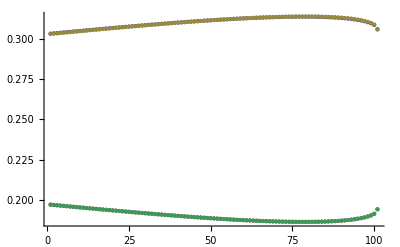

```mathematica
ListPlot[ThreeKUpperHalf]
```

```mathematica
XValues25Steps=Monitor[(Simplify[Last[#]])&/@
CumulativeMean[Transpose[
LQRWHistorgramPositionProbabilities[
SparseArray[
{{12,1}->0,
{1,1}->x,
{2,1}->Sqrt[(1-x^2)/2],
{3,1}->Sqrt[(1-x^2)/2]}
],
25]]],j];
```

```mathematica
XValues5Steps={1/2916((1240 x+(193+57 ⅈ √3) √(2-2 x^2)) Conjugate[x]+(√2 (193-57 ⅈ √3) x+1316 √(1-x^2)) Conjugate[√(1-x^2)]),((574 x+(-29-3 ⅈ √3) √(2-2 x^2)) Conjugate[x]+(-29 √2 x+3 ⅈ √6 x+572 √(1-x^2)) Conjugate[√(1-x^2)])/2916,1/972 ((176 x+(-45-17 ⅈ √3) √(2-2 x^2)) Conjugate[x]+(-45 √2 x+17 ⅈ √6 x+152 √(1-x^2)) Conjugate[√(1-x^2)]),((574 x+(-29-3 ⅈ √3) √(2-2 x^2)) Conjugate[x]+(-29 √2 x+3 ⅈ √6 x+572 √(1-x^2)) Conjugate[√(1-x^2)])/2916};XValues10Steps={1/433026((143578 x+(12743+2685 ⅈ √3) √(2-2 x^2)) Conjugate[x]+(√2 (12743-2685 ⅈ √3) x+173802 √(1-x^2)) Conjugate[√(1-x^2)]),1/1299078((274390 x+(-25643+1779 ⅈ √3) √(2-2 x^2)) Conjugate[x]+(-25643 √2 x-1779 ⅈ √6 x+248612 √(1-x^2)) Conjugate[√(1-x^2)]),1/1299078((319564 x+(13057-11613 ⅈ √3) √(2-2 x^2)) Conjugate[x]+(√2 (13057+11613 ⅈ √3) x+280448 √(1-x^2)) Conjugate[√(1-x^2)]),1/1299078((274390 x+(-25643+1779 ⅈ √3) √(2-2 x^2)) Conjugate[x]+(-25643 √2 x-1779 ⅈ √6 x+248612 √(1-x^2)) Conjugate[√(1-x^2)])};XValues15Steps={1/229582512((58858280 x+(3967373-66303 ⅈ √3) √(2-2 x^2)) Conjugate[x]+(√2 (3967373+66303 ⅈ √3) x+70916158 √(1-x^2)) Conjugate[√(1-x^2)]),1/57395628((11230067 x+(-1006270+209307 ⅈ √3) √(2-2 x^2)) Conjugate[x]+(-1006270 √2 x-209307 ⅈ √6 x+11042599 √(1-x^2)) Conjugate[√(1-x^2)]),1/76527504((26961232 x+(1360929-536051 ⅈ √3) √(2-2 x^2)) Conjugate[x]+(√2 (1360929+536051 ⅈ √3) x+23441854 √(1-x^2)) Conjugate[√(1-x^2)]),1/57395628((11230067 x+(-1006270+209307 ⅈ √3) √(2-2 x^2)) Conjugate[x]+(-1006270 √2 x-209307 ⅈ √6 x+11042599 √(1-x^2)) Conjugate[√(1-x^2)])};XValues20Steps={1/48814981614((14639450582 x+(538342683-580817483 ⅈ √3) √(2-2 x^2)) Conjugate[x]+(√2 (538342683+580817483 ⅈ √3) x+14732557022 √(1-x^2)) Conjugate[√(1-x^2)]),1/292889889684((55113457748 x+(-3320735503+1013834739 ⅈ √3) √(2-2 x^2)) Conjugate[x]+(-3320735503 √2 x-1013834739 ⅈ √6 x+60765549706 √(1-x^2)) Conjugate[√(1-x^2)]),1/73222472421((23706567674 x+(852853727+364308855 ⅈ √3) √(2-2 x^2)) Conjugate[x]+(√2 (852853727-364308855 ⅈ √3) x+20740862035 √(1-x^2)) Conjugate[√(1-x^2)]),1/292889889684((55113457748 x+(-3320735503+1013834739 ⅈ √3) √(2-2 x^2)) Conjugate[x]+(-3320735503 √2 x-1013834739 ⅈ √6 x+60765549706 √(1-x^2)) Conjugate[√(1-x^2)])};XValues25Steps={1/44059007691036((13600966413736 x+(909348871597-293451767409 ⅈ √3) √(2-2 x^2)) Conjugate[x]+(√2 (909348871597+293451767409 ⅈ √3) x+12524480970704 √(1-x^2)) Conjugate[√(1-x^2)]),1/44059007691036((8591380373986 x+(-454792728800+112404604443 ⅈ √3) √(2-2 x^2)) Conjugate[x]+(-454792728800 √2 x-112404604443 ⅈ √6 x+9482804681909 √(1-x^2)) Conjugate[√(1-x^2)]),1/14686335897012((4425093509776 x+(78862001+22880852841 ⅈ √3) √(2-2 x^2)) Conjugate[x]+(√2 (78862001-22880852841 ⅈ √3) x+4189639118838 √(1-x^2)) Conjugate[√(1-x^2)]),1/44059007691036((8591380373986 x+(-454792728800+112404604443 ⅈ √3) √(2-2 x^2)) Conjugate[x]+(-454792728800 √2 x-112404604443 ⅈ √6 x+9482804681909 √(1-x^2)) Conjugate[√(1-x^2)])};XValues50Steps={1/12204265790761494009094233((3733813360997106476029621 x+(231343705546849607195538-85390002181944248470555 ⅈ √3) √(2-2 x^2)) Conjugate[x]+(√2 (231343705546849607195538+85390002181944248470555 ⅈ √3) x+3605757118497280729185196 √(1-x^2)) Conjugate[√(1-x^2)]),1/36612797372284482027282699((7257833657161313301546137 x+(-412246020077758554760918+105219547956144337970811 ⅈ √3) √(2-2 x^2)) Conjugate[x]+(-412246020077758554760918 √2 x-105219547956144337970811 ⅈ √6 x+7689946449813757891113796 √(1-x^2)) Conjugate[√(1-x^2)]),1/36612797372284482027282699((10895689974970535996101562 x+(130460923514968287935222+45730910633544069470043 ⅈ √3) √(2-2 x^2)) Conjugate[x]+(√2 (130460923514968287935222-45730910633544069470043 ⅈ √3) x+10415633117165124057499519 √(1-x^2)) Conjugate[√(1-x^2)]),1/36612797372284482027282699((7257833657161313301546137 x+(-412246020077758554760918+105219547956144337970811 ⅈ √3) √(2-2 x^2)) Conjugate[x]+(-412246020077758554760918 √2 x-105219547956144337970811 ⅈ √6 x+7689946449813757891113796 √(1-x^2)) Conjugate[√(1-x^2)])};
XValues100Steps={((10481565064819900516512809752219627054109344385206 x+(401534391075291464049432941343076313888193509021-49353013071056124317028836285210941314923524641 ⅈ √3) √(2-2 x^2)) Conjugate[x]+(√2 (401534391075291464049432941343076313888193509021+49353013071056124317028836285210941314923524641 ⅈ √3) x+10148603270190287823622649311134698269375179818466 √(1-x^2)) Conjugate[√(1-x^2)])/34702086395955429623121716070885165695275239814734,((40233878830081044605609077548433571190910847687684 x+(-2466541413608611250300857683283736944112262934111+525229499211942941606821177275295969617629359107 ⅈ √3) √(2-2 x^2)) Conjugate[x]+(-2466541413608611250300857683283736944112262934111 √2 x-525229499211942941606821177275295969617629359107 ⅈ √6 x+44390221074875396196088956243582117894542150500906 √(1-x^2)) Conjugate[√(1-x^2)])/208212518375732577738730296425310994171651438888404,(2 (8106921290831385678554410351890761183146709650225 x+2 (157742280047842107269069857406813500305960300881-47146307499846821081966833552457893209107348148 ⅈ √3) √(2-2 x^2)) Conjugate[x]+(4 √2 (157742280047842107269069857406813500305960300881+47146307499846821081966833552457893209107348148 ⅈ √3) x+14635114151210014601204122017834642191579014743949 √(1-x^2)) Conjugate[√(1-x^2)])/52053129593933144434682574106327748542912859722101,((40233878830081044605609077548433571190910847687684 x+(-2466541413608611250300857683283736944112262934111+525229499211942941606821177275295969617629359107 ⅈ √3) √(2-2 x^2)) Conjugate[x]+(-2466541413608611250300857683283736944112262934111 √2 x-525229499211942941606821177275295969617629359107 ⅈ √6 x+44390221074875396196088956243582117894542150500906 √(1-x^2)) Conjugate[√(1-x^2)])/208212518375732577738730296425310994171651438888404};
```

```mathematica
XValues500Steps={((3731818945917164564105077289342823018530949362240671502599699555908879882993434314139000524837596752347580612383378283796307082320730167259411896907778416804502126774122413033238479146951192989343671765985634261687424799607196693586309107990 x+(130483386070789454872174880164683574952250679035003873934365105114883470062354558385855171326117777551949995469381307601720288314960327707139700807370760938530066910340668618134410726907851758093873807050360880231376974591545229910207202935-30924294896318777509063604730623387401756426042956524406146485184019420068104209018654495944618899828889782943627047122705980812776677260078710168745768239893402058646746850498971331702956136252551570325506202562175783635642388508337660831 ⅈ √3) √(2-2 x^2)) Conjugate[x]+(√2 (130483386070789454872174880164683574952250679035003873934365105114883470062354558385855171326117777551949995469381307601720288314960327707139700807370760938530066910340668618134410726907851758093873807050360880231376974591545229910207202935+30924294896318777509063604730623387401756426042956524406146485184019420068104209018654495944618899828889782943627047122705980812776677260078710168745768239893402058646746850498971331702956136252551570325506202562175783635642388508337660831 ⅈ √3) x+3473829426508973350383753961369767274772517650128667532195439605257759217591132828773366931072349843356081778153540764666832687706241733222083866567206929942416229123599152500131876706527900338305637185198985541069186896597101726332117894486 √(1-x^2)) Conjugate[√(1-x^2)])/12144337459820558905356679204567468585419810598684542095475575968081920463989021091722301759835115853624932020646490887821453881126682364091759471926131716610527271596781112912341864507412981612130845184111110961295154800920706691656121740334,((14118991206600219272059203677912294226015632010773427512681257728351299146358839042205350567236205750653786015411618807579618912735036922300998621447724020965517913012021549110805952010438764843900878125852316565869425072181125485194571926388 x+(-778613076636934144610912011928421051146501148113984743264571562243881150133591041316462669511175451225589678547397304554813991588999820173266831279931884489316008206351948096133089320569178829153100793914328389722605271916415704672162929551+193947521398368342999838825047388666318954115345925135114162889063659101835836426590759432381719879825943505493718251839578641893814613630572876719834575800375131123478377104397046189909856856060423163144849109445727564747735317614676136627 ⅈ √3) √(2-2 x^2)) Conjugate[x]+(-778613076636934144610912011928421051146501148113984743264571562243881150133591041316462669511175451225589678547397304554813991588999820173266831279931884489316008206351948096133089320569178829153100793914328389722605271916415704672162929551 √2 x-193947521398368342999838825047388666318954115345925135114162889063659101835836426590759432381719879825943505493718251839578641893814613630572876719834575800375131123478377104397046189909856856060423163144849109445727564747735317614676136627 ⅈ √6 x+15669568886844789200765804585254509527480187656308113945357087963359019899980400770897703640755715937601767534499505163657501626584496811559696123458357270299608881044253628868661058457103346136679293424091407087595352689943187667717370706186 √(1-x^2)) Conjugate[√(1-x^2)])/72866024758923353432140075227404811512518863592107252572853455808491522783934126550333810559010695121749592123878945326928723286760094184550556831556790299663163629580686677474051187044477889672785071104666665767770928805524240149936730442004,((5559282167554981875847801033880821237325475849279092132973185754083911298313960645272276568878175776589134104688859502247910741841409834098022051803667939226278760727977275263252102035473300512230321064262056766476882465879702254507432985322 x+(193581459212282889997193685717185163144874555504486560730738123449615369973263683079448577766411059284869846069626690874826563322059418525923864428909800836862903737664971120864928569922811777435739686381622874514237174070890007470770660373-50587318354706005236324005427759252056842418608527780947861716755800420815761899767397972273931590169637078331418555235730349727742290925168373106798635540347462473769068276450066097400494223651384226084165250879600106920404076044831577067 ⅈ √3) √(2-2 x^2)) Conjugate[x]+(√2 (193581459212282889997193685717185163144874555504486560730738123449615369973263683079448577766411059284869846069626690874826563322059418525923864428909800836862903737664971120864928569922811777435739686381622874514237174070890007470770660373+50587318354706005236324005427759252056842418608527780947861716755800420815761899767397972273931590169637078331418555235730349727742290925168373106798635540347462473769068276450066097400494223651384226084165250879600106920404076044831577067 ⅈ √3) x+5170977606544983732076485572169297202230845594679754872241660562556731919606632008974550422766291046602391596489672602903180976838412540524665346309208544852362123187646126183984452472775948842398165286322484586541275511513813614127320415679 √(1-x^2)) Conjugate[√(1-x^2)])/18216506189730838358035018806851202878129715898026813143213363952122880695983531637583452639752673780437398030969736331732180821690023546137639207889197574915790907395171669368512796761119472418196267776166666441942732201381060037484182610501,((14118991206600219272059203677912294226015632010773427512681257728351299146358839042205350567236205750653786015411618807579618912735036922300998621447724020965517913012021549110805952010438764843900878125852316565869425072181125485194571926388 x+(-778613076636934144610912011928421051146501148113984743264571562243881150133591041316462669511175451225589678547397304554813991588999820173266831279931884489316008206351948096133089320569178829153100793914328389722605271916415704672162929551+193947521398368342999838825047388666318954115345925135114162889063659101835836426590759432381719879825943505493718251839578641893814613630572876719834575800375131123478377104397046189909856856060423163144849109445727564747735317614676136627 ⅈ √3) √(2-2 x^2)) Conjugate[x]+(-778613076636934144610912011928421051146501148113984743264571562243881150133591041316462669511175451225589678547397304554813991588999820173266831279931884489316008206351948096133089320569178829153100793914328389722605271916415704672162929551 √2 x-193947521398368342999838825047388666318954115345925135114162889063659101835836426590759432381719879825943505493718251839578641893814613630572876719834575800375131123478377104397046189909856856060423163144849109445727564747735317614676136627 ⅈ √6 x+15669568886844789200765804585254509527480187656308113945357087963359019899980400770897703640755715937601767534499505163657501626584496811559696123458357270299608881044253628868661058457103346136679293424091407087595352689943187667717370706186 √(1-x^2)) Conjugate[√(1-x^2)])/72866024758923353432140075227404811512518863592107252572853455808491522783934126550333810559010695121749592123878945326928723286760094184550556831556790299663163629580686677474051187044477889672785071104666665767770928805524240149936730442004};
```

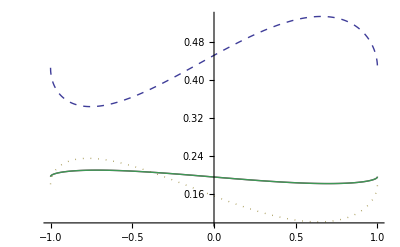
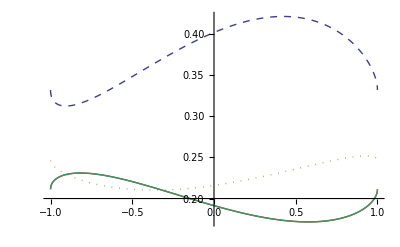
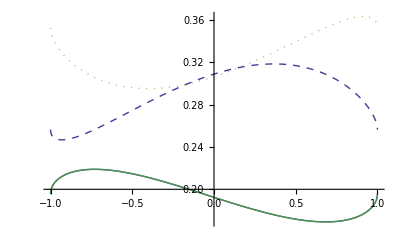
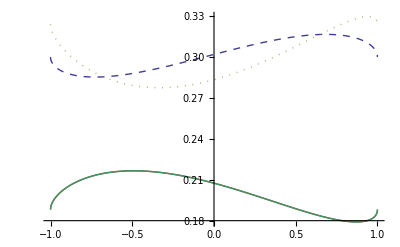
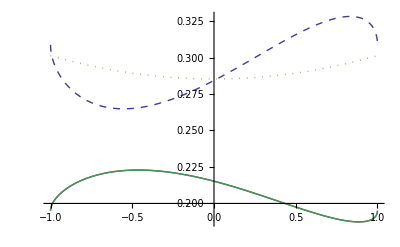
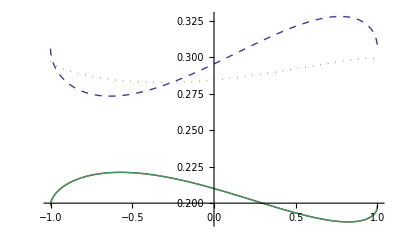
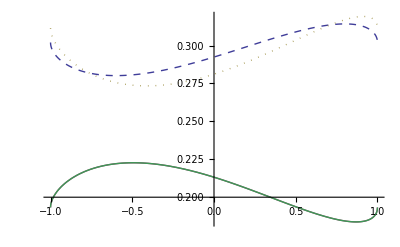
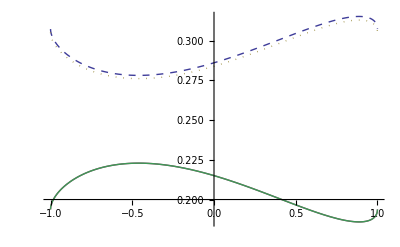

```mathematica
Table[
Plot[v,{x,-1,1},
PlotStyle->{Dashed,Thin,Dotted,Thin}],
{v,{XValues5Steps,XValues10Steps,XValues15Steps,XValues20Steps,XValues25Steps,XValues50Steps,XValues100Steps,XValues500Steps}}]
```